```mathematica
MaxVoltage =4.9; 
OverdriveFactor= 1;
ControllerFrequency =1000;
ControllerPrecision = 2^8;
Vold[t_]:=Vextern[t-1/FrameRate]
Vnew[t_]:=Vextern[t]
FrameTime[t_]:=1/FrameRate Mod[ FrameRate t,1]
t1[t_]:=Ceiling[OverdriveFactor*τc[t]Log[(MaxVoltage^2-Vold[t]^2)/(MaxVoltage^2-Vnew[t]^2)],1/ControllerFrequency]
t2[t_]:=Ceiling[τc[t]Log[Vold[t]^2/Vextern[t]^2],1/ControllerFrequency]

HighVoltage[t_]:=√((Vnew[t]^2-Vold[t]^2 ⅇ^((-t1[t])/τc[t]))/(1-ⅇ^((-t1[t])/τc[t])))
LowVoltage[t_]:=√((Vnew[t]^2-Vold[t]^2 ⅇ^((-t2[t])/τc[t]))/(1-ⅇ^((-t2[t])/τc[t])))
Overdrive[t_]:=Piecewise[{{Vextern[t], FrameTime[t]==0}, {OverdriveFactor*HighVoltage[t]+(1-OverdriveFactor)Vextern[t], Vnew[t]>Vold[t] &&FrameTime[t]<t1[t]}, {OverdriveFactor*LowVoltage[t]+(1-OverdriveFactor)Vextern[t], Vnew[t]<Vold[t]&&FrameTime[t]<t2[t]}, {Vextern[t], True}}]
Plot[Overdrive[t],{t,0,5/FrameRate},AxesOrigin->{0,0},PlotPoints->10];
Vnow[t_]:=√(Vold[t]^2+(Vnew[t]^2-Vold[t]^2)(1-ⅇ^((-FrameTime[t])/τc[t])))
Plot[{Overdrive[t],Vnow[t]},{t,0,5/FrameRate}]
```

Plot::plln: Limiting value 5/FrameRate in {t, 0, 5/FrameRate} is not a machine-sized real number.

Plot[{Overdrive[t],Vnow[t]},{t,0,5/FrameRate}]

```mathematica
StepResponse[t_,τ_]:=Piecewise[{{√(1-ⅇ^(-t/τ)), 0<t<10τ}, {1, True}}]
ImpulseResponse[t_,τ_]:=Piecewise[{{ⅇ^(-t/τ)/(2τ √(1-ⅇ^(-t/τ))), 0<t<10τ}, {0, True}}]
StepResponseq[t_,τ_]:=Piecewise[{{(1-ⅇ^(-t/τ)), 0<t<10τ}, {1, True}}]
ImpulseResponseq[t_,τ_]:=Piecewise[{{ⅇ^(-t/τ)/τ, 0<t<10τ}, {0, True}}]
PixelSpeed  :=0.0029;
FrameRate = 100;
```

```mathematica
Plot[ImpulseResponse[t,PixelSpeed],{t,0,5/100}]
```

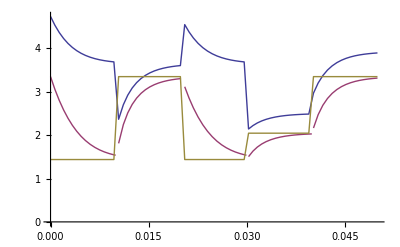

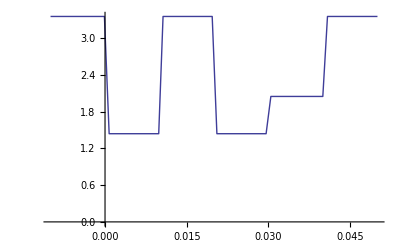

```mathematica
ds[τ_] := {s,0}~Join~ Table[(k-1)/ControllerFrequency,{k,2,ControllerFrequency}]~Join~ Table[k/FrameRate,{k,0,5}]~Join~{10 τ}
(*VVpixel[t_,τ_]:= √(4+NIntegrate[ImpulseResponse[s,τ]*√5 UnitStep[ t-s],{s,0,10τ}]^2)
Vpixel[t_,τ_]:= √(Vnew[t]^2+Sign[Vnew[t]-Vold[t]] NIntegrate[ImpulseResponse[s,τ]*√Abs[Vnew[ t-s]^2-Vold[t-s]^2],{s,0,10τ}]^2)

Vnow[t_,τ_]:=√(4+(9-4)(1-ⅇ^(-t/τ)))*)
sa[t_]:=Sign[Vnew[t]-Vold[t]];
diff[t_]:=Vnew[t]^2-Vold[t]^2

Vpixel[t_,τ_]:=√(Vold[t]^2+NIntegrate[ImpulseResponseq[s,τ]*(Vnew[t-s])^2,{s,0,10τ}])
Vnow[t_,τ_]:=√(4-(4-9)(1-ⅇ^(-t/τ)))

Plot[{Vpixel[t,PixelSpeed],Vnow[t],Vnew[t]},{t,0,5/FrameRate}, AxesOrigin->{0,0},PlotPoints->10,MaxRecursion->3]
Plot[Vnew[t],{t,-1/FrameRate,5/FrameRate}, AxesOrigin->{0,0},PlotPoints->10,MaxRecursion->3]
```

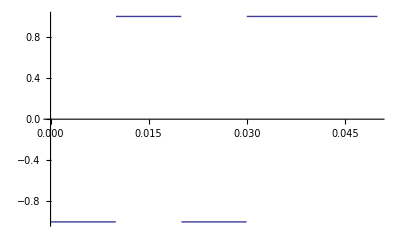

```mathematica
Manipulate[sa[k/FrameRate],{k,0,5}]
Plot[sa[t],{t,0,5/FrameRate}, AxesOrigin->{0,0}]
```

```mathematica
Vpixel[0.5/FrameRate,PixelSpeed]-Vnow[0.5/FrameRate,PixelSpeed]
```

-0.288175

```mathematica
(*GTG correction, from second paper*)
Lh[t_]:=Max[Abs[T[Vextern[t-1/FrameRate]]],Abs[T[Vextern[t]]]](*Higher Grey level*)
Ll[t_]:=Min[Abs[T[Vextern[t-1/FrameRate]]],Abs[T[Vextern[t]]]] (*Lower Grey level*)
Delta[t_]:=(Ll[t]/Lh[t])^0.45;
τc[t_]:=PixelSpeed(*PixelSpeed/(4 Log[3])Log[1+16/(1.8*Delta[t]+0.2)](*GTG correction*)*)
```

```mathematica
Signal[t_]:=UnitBox[FrameRate t-0.5]+UnitBox[FrameRate t-2.5]+1/2 UnitBox[FrameRate t-3.5]

(*Overdrive Algorithm*)
Vextern[t_]:=V[Transmission*Signal[t]+Transmission/ContrastRatio] (*no overdrive*)
ContrastRatio := 200.0;
Transmission := 0.9;
T[V_]:=(1-Tanh[2V-4])/2(*Roungh Transmission vs internal voltage fit*)
V[T_]:=1/2 (4+ArcTanh[1-2 T]) (*Inverse of the above*)
```

-2